## Location Statistics

```mathematica
data={17,18,19,19,20,21,22,23,24,26,27,28,29,30,32,34,35,37,39,42,45,50,58,64,75};
```

```mathematica
Mean[data]
```

834/25

```mathematica
Median[data]
```

29

```mathematica
Commonest[data]
```

{19}

```mathematica
TrimmedMean[data]
```

742/23

```mathematica
WinsorizedMean[data]
```

824/25

```mathematica
BiweightLocation[data]
```

30.2025

```mathematica
SpatialMedian[data]
```

29

```mathematica
CentralFeature[data]
```

29

```mathematica
HarmonicMean[data]
```

1723526276472000/60738611728073

```mathematica
GeometricMean[data]
```

2 3^(13/25) 5^(8/25) 7^(4/25) 18722^(1/25) 121771^(2/25)

```mathematica
ContraharmonicMean[data]
```

16682/417

## Dispersion Statistics

```mathematica
Variance[data]
```

17318/75

```mathematica
TrimmedVariance[data]
```

40393/253

```mathematica
WinsorizedVariance[data]
```

19629/100

```mathematica
StandardDeviation[data]
```

(√(17318/3))/5

```mathematica
MeanDeviation[data]
```

1454/125

```mathematica
MedianDeviation[data]
```

8

```mathematica
QuartileDeviation[data]
```

9

```mathematica
InterquartileRange[data]
```

18

```mathematica
QnDispersion[data]
```

12.6088

```mathematica
SnDispersion[data]
```

12.3714

```mathematica
BiweightMidvariance[data]
```

48042166611270066125/270395940895233409

## Shape Statistics

```mathematica
Skewness[data]
```

31392729/(277088 √8659)

```mathematica
Kurtosis[data]
```

2604583489/685515712

```mathematica
QuartileSkewness[data]
```

7/36

```mathematica
Entropy[data]
```

-(2 Log[2])/25+Log[25]

```mathematica
EstimatedDistribution[data,GammaDistribution[α,β]]
```

GammaDistribution[5.95703,5.60011]

```mathematica
EstimatedDistribution[data,NormalDistribution[α,β]]
```

NormalDistribution[33.36,14.8886]

## Dependency Statistics

```mathematica
Covariance[data]
```

17318/75

```mathematica
Correlation[data]
```

1

```mathematica
AbsoluteCorrelation[data]
```

33364/25

```mathematica
SpearmanRho[data]
```

1

```mathematica
KendallTau[data]
```

1

```mathematica
HoeffdingD[data]
```

51269/51520

```mathematica
GoodmanKruskalGamma[data]
```

1

```mathematica
BlomqvistBeta[data]
```

1

```mathematica
WilksW[data]
```

1

```mathematica
PillaiTrace[data]
```

1

## Spatial Point Statistics

This does not apply

## General Statistics

```mathematica
Moment[data]
```

Moment[{17,18,19,19,20,21,22,23,24,26,27,28,29,30,32,34,35,37,39,42,45,50,58,64,75}]

```mathematica
?Moment
```

```mathematica
Moment[data,1]
```

834/25

```mathematica
Moment[data,2]
```

33364/25

```mathematica
Moment[data,3]
```

1583226/25

```mathematica
Moment[data,4]
```

86039644/25

```mathematica
Moment[data,5]
```

5145294834/25

```mathematica
?CentralMoment
```

```mathematica
??CentralMoment
```

```mathematica
CentralMoment[data,1]
```

0

```mathematica
CentralMoment[data,2]
```

138544/625

```mathematica
CentralMoment[data,3]
```

62785458/15625

```mathematica
CentralMoment[data,4]
```

72928337692/390625

```mathematica
CentralMoment[data,5]
```

61888928459946/9765625

```mathematica
??FactorialMoment
```

```mathematica
FactorialMoment[data,1]
```

834/25

```mathematica
FactorialMoment[data,2]
```

6506/5

```mathematica
FactorialMoment[data,3]
```

1484802/25

```mathematica
FactorialMoment[data,4]
```

76902288/25

```mathematica
FactorialMoment[data,5]
```

867732624/5

```mathematica
??Cumulant
```

```mathematica
Cumulant[data,1]
```

834/25

```mathematica
Cumulant[data,2]
```

138544/625

```mathematica
Cumulant[data,3]
```

62785458/15625

```mathematica
Cumulant[data,4]
```

15345017884/390625

```mathematica
Cumulant[data,5]
```

-25096556471574/9765625

```mathematica
??RootMeanSquare
```

```mathematica
RootMeanSquare[data]
```

(2 √8341)/5

```mathematica
Expectation[x==19,x\[Distributed]data]
```

1/25 (23 False+2 True)

```mathematica
Expectation[x>19,x\[Distributed]data]
```

1/25 (4 False+21 True)

```mathematica
Expectation[x<19,x\[Distributed]data]
```

1/25 (23 False+2 True)

```mathematica
Expectation[x<=19,x\[Distributed]data]
```

1/25 (21 False+4 True)

```mathematica
Expectation[x>=19,x\[Distributed]data]
```

1/25 (2 False+23 True)

```mathematica
Expectation[x!=19,x\[Distributed]data]
```

1/25 (2 False+23 True)

```mathematica
Probability[x==19,x\[Distributed]data]
```

2/25

```mathematica
Probability[x>19,x\[Distributed]data]
```

21/25

```mathematica
Probability[x<19,x\[Distributed]data]
```

2/25

```mathematica
?BinCounts
```

```mathematica
BinCounts[data]
```

{0,1,1,2,1,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1}

## Order Statistics

```mathematica
Min[data]
```

17

```mathematica
Max[data]
```

75

```mathematica
MinMax[data]
```

{17,75}

```mathematica
Sort[data]
```

{17,18,19,19,20,21,22,23,24,26,27,28,29,30,32,34,35,37,39,42,45,50,58,64,75}

```mathematica
Ordering[data]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
RankedMin[data,1]
```

17

```mathematica
RankedMin[data,4]
```

19

```mathematica
?Quantile
```

```mathematica
Quantile[data,Subdivide[10]]
```

{17,19,20,23,26,29,32,37,42,58,75}

```mathematica
Quantile[data,Subdivide[100]]
```

{17,17,17,17,17,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,21,21,21,21,22,22,22,22,23,23,23,23,24,24,24,24,26,26,26,26,27,27,27,27,28,28,28,28,29,29,29,29,30,30,30,30,32,32,32,32,34,34,34,34,35,35,35,35,37,37,37,37,39,39,39,39,42,42,42,42,45,45,45,45,50,50,50,50,58,58,58,58,64,64,64,64,75,75,75,75}

```mathematica
?Quartiles
```

```mathematica
Quartiles[data]
```

{87/4,29,159/4}

```mathematica
TakeLargest[data,1]
```

{75}

```mathematica
TakeLargest[data,4]
```

{75,64,58,50}

```mathematica
TakeSmallest[data,3]
```

{17,18,19}

## Data Models

```mathematica
WeightedData[]
```

## Symbolic Features of Distributions

```mathematica
?CDF
```

```mathematica
EstimatedDistribution[data,NormalDistribution[a,b]]
```

NormalDistribution[33.36,14.8886]

```mathematica
CDF[EstimatedDistribution[data,NormalDistribution[a,b]]]
```

Function[x,1/2 Erfc[0.0474932 (33.36-x)]]

```mathematica
PDF[EstimatedDistribution[data,NormalDistribution[a,b]]]
```

Function[x,0.0267952 ⅇ^(-0.0022556 (-33.36+x)^2)]

```mathematica
InverseCDF[EstimatedDistribution[data,NormalDistribution[a,b]],t]
```

ConditionalExpression[33.36-21.0557 InverseErfc[2 t], 0≤t≤1]

```mathematica
?CharacteristicFunction
```

```mathematica
CharacteristicFunction[EstimatedDistribution[data,NormalDistribution[a,b]],t]
```

ⅇ^((0.+33.36 ⅈ) t-110.835 t^2)

## Statistical Visualization

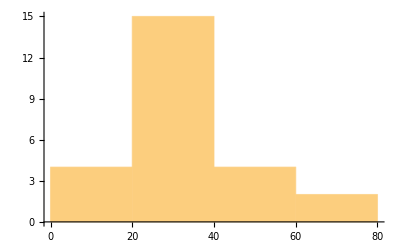

```mathematica
Histogram[data]
```

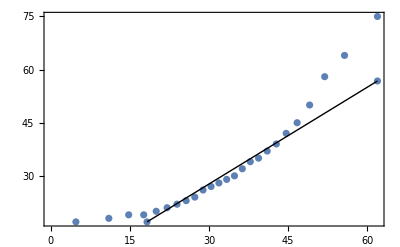

```mathematica
QuantilePlot[data]
```

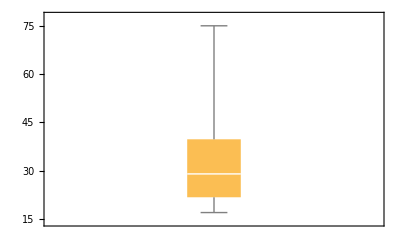

```mathematica
BoxWhiskerChart[data]
```

## Robust Shapes Measures

```mathematica
?FindDistributionParameters
```

```mathematica
FindDistributionParameters[data,EstimatedDistribution[data,NormalDistribution[a,b]]]
```

{}

## Special Moments

```mathematica
?PowerSymmetricPolynomial
```

```mathematica
PowerSymmetricPolynomial[4,data]
```

86039644

```mathematica
AugmentedSymmetricPolynomial[4,data]
```

1

```mathematica
FindDistribution[data]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

WeibullDistribution[0.826219,15.5643,17.3766]